# Preparations

```mathematica
<<ToCVXPY`
```

ToCVXPY beta 1.2.0

------------------

Use GenerateTask[target, allVars, sdpMatrix, loopEquations, para, lambda, eps]

to create Task.json in order to transport the SDP question into CVXPY

Parameter:

target: The coefficients of the target function.

{1, 0, 2} will give allVars[1] + 2 allVars[3] as target.

allVars: All the variables shown in this SDP problem.

sdpMatrix: SDP Matrix as constrains.

loopEquations: Equations constrains. Can include a parameter.

para: The parameter shown in loopEquations.

lambda: The discrete values of para.

eps: The threshold of the SDP algorithm. It must be in the interval [10^-9, 10^-3]

------------------

DREAM @ 20240603

## Edge and Coordinate representations, and Plot loop

We usually use “edge-representation” for Wilson loop, such as {a,b,-a,-b}.  
To plot a loop as well as some other cases, it is useful to use the “coordinate-representation”, in which we give the coordinate for the vertices. 
Below we obtain coordinate-representation from the edge-representation, and then plot the loop using coordinate-representation.

```mathematica
(* From edge to coordinate representation *)
```

```mathematica
EdgesToCoordinates2D[edges_List]:=Module[{pos={0,0},coords={{0,0}}},
Scan[(pos=pos+Switch[#,a,{1,0},b,{0,1},-a,{-1,0},-b,{0,-1}];
AppendTo[coords,pos])&,edges];
If[Last[coords]===First[coords],Drop[coords,-1],"NonClosedLoop"]]
```

```mathematica
EdgesToCoordinates3D[edges_List]:=Module[{pos={0,0,0},coords={{0,0,0}}},
Scan[(pos=pos+Switch[#,a,{1,0,0},b,{0,1,0},c,{0,0,1},-a,{-1,0,0},-b,{0,-1,0},-c,{0,0,-1}];
AppendTo[coords,pos])&,edges];
If[Last[coords]===First[coords],Drop[coords,-1],"NonClosedLoop"]]
```

```mathematica
EdgesToCoordinates2D[{a,b,-a,-b}]
EdgesToCoordinates3D[{a,b,-a,-b}]
```

{{0,0},{1,0},{1,1},{0,1}}

{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}

```mathematica
(* Plot loop using coordinate representation *)
```

```mathematica
plotLoopCoord[coords_List]:=Module[{dim},
dim=Length[coords[[1]]];
If[dim==2,Graphics[{Arrow/@Partition[Append[coords,First[coords]],2,1],Red,PointSize[Small],Point[coords]},Axes->False],If[dim==3,Graphics3D[{Arrow/@Partition[Append[coords,First[coords]],2,1],Red,PointSize[Small],Point[coords]},Axes->False]]]]
```

```mathematica
plotLoopEdges2D[edges_List]:=Module[{coords=EdgesToCoordinates2D[edges]},
plotLoopCoord[coords]]
```

```mathematica
plotLoopEdges3D[edges_List]:=Module[{coords=EdgesToCoordinates3D[edges]},
plotLoopCoord[coords]]
```

```mathematica
plotLoopEdges3D[{a,a,b,a,b,-a,-b,-a,-a,-b}]
```

-Graphics3D-

## Symmetry operation for ladder-type operators

We consider the symmetry  operation for the paths and loops.

### Path

Path operators are used to generate positive matrices by sewing them to loops.
Different edge lists give different paths.
From one path, we can generate three different paths by conjugate, reflection, and conjugate-reflection.

```mathematica
(* operation on Path operators *)
```

```mathematica
reflecta[w_]:=w/.{a->-a,-a->a};
reflectb[w_]:=w/.{b->-b,-b->b};
reflectab[w_]:=w/.{a->-a,-a->a,b->-b,-b->b};
```

```mathematica
conjugate[w_]:=Reverse[w]//reflectab
reflectconjugate[w_]:=Reverse[w]//reflectb
```

```mathematica
(* example *)
```

```mathematica
{a,b,-a,-b}//reflecta
{a,b,-a,-b}//conjugate
{a,b,-a,-b}//reflectconjugate
```

{-a,b,a,-b}

{b,a,-b,-a}

{b,-a,-b,a}

```mathematica
(* generate three other paths from one path *)
```

```mathematica
generatePathbyOper[w_]:={w,w//conjugate,w//reflecta,w//reflectconjugate}//Union;
```

```mathematica
{a,b,-a,-b}//generatePathbyOper
```

{{-a,b,a,-b},{a,b,-a,-b},{b,-a,-b,a},{b,a,-b,-a}}

### Loop

Unlike path, different loop operators can be equivalent if they are related by symmetry operators.
The symmetries include cyclicity, reversion, and lattice symmetry. 
For the ladder-type operators in 2D, we consider the sub-group of the 2D lattice, which contains only four generators. 

To remove the equivalence between different loop operators, we choose a “standard form” for a given operator.

```mathematica
(* Define a "standard" ordering by including cyclic *)
```

```mathematica
cycPerm=Partition[#,Length@#,1,{1,1}]&;
```

```mathematica
orderCyclic[edges_]:=Block[{cyclist=cycPerm[edges]},Extract[cyclist,Ordering[cyclist,1]] ];
```

```mathematica
(* Define a "standard" ordering by including cyclic and reverse *)
```

```mathematica
orderCyclicReverse[edges_]:=Sort[{orderCyclic[edges],orderCyclic[edges//Reverse]}][[1]];
```

```mathematica
(* Define a "standard" ordering by including cyclic, reverse, and symmetries *)
```

```mathematica
orderCyclicReverseSymmetry[edges_,symOper_]:=Sort[orderCyclicReverse[edges/.#]&/@symOper][[1]];
```

```mathematica
(* symmetries for the ladder-type operators in 2D *)
```

```mathematica
symOperLadder2D[{a_,b_}]:=Flatten[Table[{a->i a,b->j b,-a->-i a,-b->-j b},{i,{1,-1}},{j,{1,-1}}],1];
```

```mathematica
symOperLadder2D[{a,b}]
```

{{a→a,b→b,-a→-a,-b→-b},{a→a,b→-b,-a→-a,-b→b},{a→-a,b→b,-a→a,-b→-b},{a→-a,b→-b,-a→a,-b→b}}

```mathematica
(* reduce adjacency *)
```

```mathematica
wlred[A___,x_,-x_,B___]:=wlred[A,B]
wlred[A___,-x_,x_,B___]:=wlred[A,B]
wlred[x_,A___,-x_]:=wlred[A]
wlred[-x_,A___,x_]:=wlred[A]
```

```mathematica
redAdj[loop_List]:=List@@(wlred@@loop)
```

```mathematica
(* standard form for ladder-type loops *)
```

```mathematica
Clear[standardLadderLoop];
```

```mathematica
standardLadderLoop[{}]={};
standardLadderLoop[w_List]:=Block[{wred=w//redAdj},If[wred!={},orderCyclicReverseSymmetry[wred,symOperLadder2D[{a,b}]],wred]];
```

```mathematica
orderCyclicReverseSymmetry[{a,b,-a,-b,a,-a,a,b,-a,-b},symOperLadder2D[{a,b}]]
```

{-a,a,-a,-b,a,b,-a,-b,a,b}

```mathematica
standardLadderLoop[{a,b,-a,-b,a,-a,a,b,-a,-b}]
standardLadderLoop[{a,b,-a,-b,b,a,-b,-a}]
```

{-a,-b,a,b,-a,-b,a,b}

{}

## SD equation: SU(2)

SD in SU2:
-Graphics-
Here n_+ counts all edges that are at the same position and have same direction as μ  (including μ itself ! ), 
while n_- counts all edges that are at the same position but have operator direction as μ.

### Code for SDE

Schwinger-Dyson equation. There are two major parts:
1) from the action
2) from the splitting of repeated links

[The code we use applies to the backtrack case.]

```mathematica
WL[]=1;
```

```mathematica
(* Lagrangian contribution part: replace a link by adding a plaquette *)
(* This is the only part that depend on dimension and it is easy to generalize to 3 and 4 dim *)
```

```mathematica
(* linkNum is the position for the edge μ *)
```

```mathematica
SDEofaddPlaquette[loop_WL,linkNum_]:=Module[{linktype,ortholinks},
linktype=loop[[linkNum]];
(* find all orthogonal links *) 
ortholinks=Complement[List@@loop,{linktype,-linktype}];
(* add plaquette *)
Plus@@((ReplacePart[loop,linkNum->Sequence[linktype,#,-linktype,-#,linktype]]-ReplacePart[loop,linkNum->Sequence[#,linktype,-#]])&/@ortholinks)
]
```

```mathematica
(* Count numbers of repeated edges: n_+ and n_- *)
```

```mathematica
countRepeatLegs[loop_WL,linkNum_]:=Module[{newloop,coordloop,coordloop2,repeatlinks1,repeatlinks2},
(* change the given edge to first position *)
newloop=RotateLeft[loop,linkNum-1];
(* change edge to coordinates *)
coordloop=(List@@newloop)//EdgesToCoordinates2D;
(* define edge as a pair of coordinates *) 
coordloop2=Partition[coordloop,2,1]~Join~{{Last[coordloop],First[coordloop]}};
(* find the position of repeated edges *) 
repeatlinks1=Position[coordloop2,First[coordloop2]]//Flatten;
(* find the position of repeated edges with a minus sign *) 
repeatlinks2=Position[coordloop2,First[coordloop2]//Reverse]//Flatten;
(* give the two terms that contribute to loop equation *) 
{Length[repeatlinks1],Length[repeatlinks2]}
]
```

```mathematica
(* test example *)
```

```mathematica
countRepeatLegs[WL[a,b,-a,-b,a,b,-a,-b],2]
Subtract@@%
```

{2,0}

2

```mathematica
(* splitting loop in two parts at the repeated link at "linkNum" *)
```

```mathematica
splitLoopSU2[loop_WL,linkNum_]:=Module[{loopL,w1,w2},
loopL=List@@loop;
If[loopL[[1]]===loopL[[linkNum]],
{w1=loopL[[1;;linkNum-1]];w2=loopL[[linkNum;;Length[loopL]]];},
If[loopL[[1]]===-loopL[[linkNum]],
{w1=loopL[[1;;linkNum]];w2=loopL[[linkNum+1;;Length[loopL]]];}
]
];
Join[w1,w2//conjugate]
]
```

```mathematica
(* *)
```

```mathematica
splitLoopSU2[WL[a,b,-a,-b,a,b,-a,-b],5]
```

{a,b,-a,-b,b,a,-b,-a}

```mathematica
(* splitloop for repeated links that are same to the edge at linkNum  *)
(* the original edge is also included as a special case *)
```

```mathematica
SDEofsplitLoopSU2[loop_WL,linkNum_]:=Module[{newloop,coordloop,coordloop2,repeatlinks1,repeatlinks2},
(* change the given edge to first position *)
newloop=RotateLeft[loop,linkNum-1];
(* change edge to coordinates *)
coordloop=(List@@newloop)//EdgesToCoordinates2D;
(* define edge as a pair of coordinates *) 
coordloop2=Partition[coordloop,2,1]~Join~{{Last[coordloop],First[coordloop]}};
(* find the position of repeated edges *) 
repeatlinks1=Position[coordloop2,First[coordloop2]]//Flatten;
(* find the position of repeated edges with a minus sign *) 
repeatlinks2=Position[coordloop2,First[coordloop2]//Reverse]//Flatten;
(* give the two terms that contribute to loop equation *) 
Plus@@(WL@@splitLoopSU2[newloop,#]&/@repeatlinks1)-Plus@@(WL@@splitLoopSU2[newloop,#]&/@repeatlinks2)
(* note that the first edge is also included *)
]
```

```mathematica
SDEofsplitLoopSU2[WL[a,b,-a,-b,a,b,-a,-b],2]
SDEofsplitLoopSU2[WL[a,b,-a,-b,a,b,-a,-b],6]
```

WL[-a,b,a,-b,-a,b,a,-b]+WL[b,-a,-b,a,-a,b,a,-b]

WL[-a,b,a,-b,-a,b,a,-b]+WL[b,-a,-b,a,-a,b,a,-b]

(* the full SU(2) SD equation: add a 1/2 *)

```mathematica
SDESU2[loop_WL,linkNum_]:=SDEofaddPlaquette[loop,linkNum]+λ*(1/2 Subtract@@countRepeatLegs[loop,linkNum]*loop+SDEofsplitLoopSU2[loop,linkNum])//Expand;
```

```mathematica
(* reduce the loops to standard forms *)
```

```mathematica
SDESU2Red[loop_WL,linkNum_]:=SDESU2[loop,linkNum]/.{WL[X__]:>WL@@(List[X]//redAdj)}/.{WL[X__]:>WL@@standardLadderLoop[List[X]]}//Expand;
```

```mathematica
reduceSDE[SDE_]:=SDE/.{WL[X__]:>WL@@(List[X]//redAdj)}/.{WL[X__]:>WL@@standardLadderLoop[List[X]]}
```

```mathematica
(* plot a SDE *)
```

```mathematica
plotSDE[SDE_]:=SDE/.{WL[X__]:>(List[X]//plotLoopEdges2D)}
```

### Examples

```mathematica
(* test *)
```

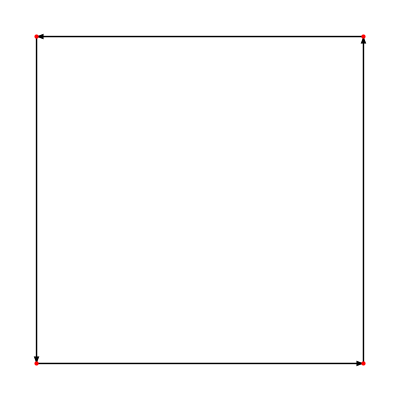
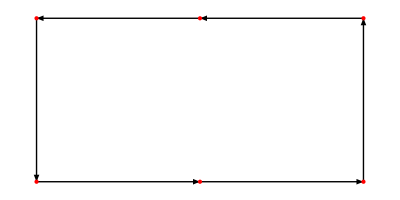
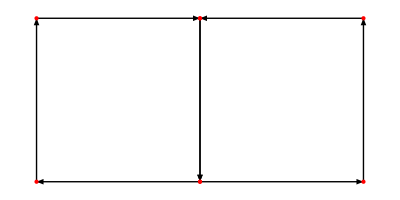
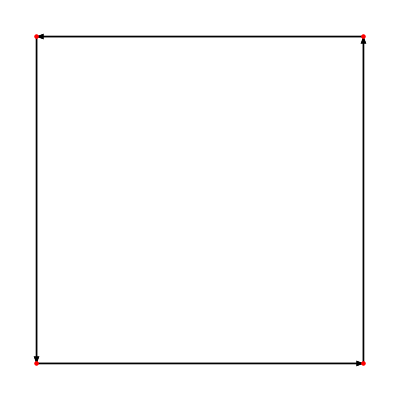
-1+(3 λ -Graphics-)/2--Graphics-+-Graphics-+-Graphics-

-1+(3 λ -Graphics-)/2--Graphics-+-Graphics-+-Graphics-

```mathematica
SDESU2[WL@@{a,b,-a,-b},2];
SDESU2Red[WL@@{a,b,-a,-b},2];
%//plotSDE
SDESU2Red[WL@@{a,b,-a,-b},4];
%//plotSDE
```

```mathematica
(* *)
```

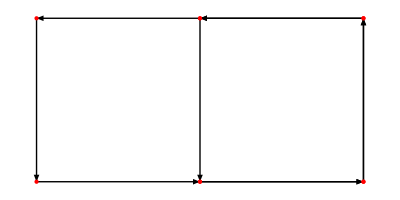
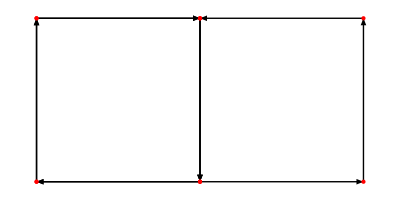
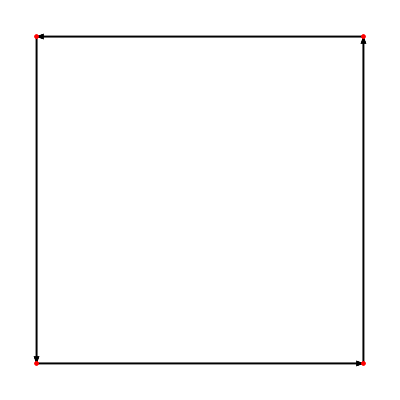
λ--Graphics-+2 λ -Graphics---Graphics-+-Graphics-+-Graphics-

```mathematica
SDESU2[WL@@{a,b,-a,-b,a,b,-a,-b},2]//reduceSDE//Expand;
%//plotSDE
```

-2 -Graphics-+λ -Graphics-+2 λ -Graphics-+2 -Graphics-

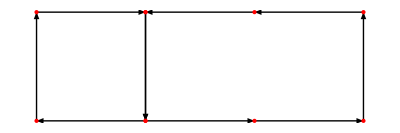
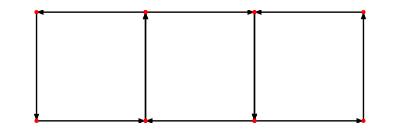
--Graphics-+(3 λ -Graphics-)/2--Graphics-+-Graphics-+-Graphics-

```mathematica
SDESU2Red[WL@@{a,b,a,-b,-a,b,-a,-b},2];
%//plotSDE
SDESU2Red[WL@@{a,b,a,-b,-a,b,-a,-b},4];
%//plotSDE
```

# Ladder-type Positivity

## Generate paths of ladder-type

```mathematica
(* Generate Path with equal number of a and b *)
```

```mathematica
Wab[0,0]={{Id}};
```

```mathematica
Wab[n_,n_]:=Block[{alists=Prepend[#,a]&/@Permutations[Join[Table[a,n-1],Table[-a,n]]],blist=Flatten[Table[{b,-b},n]]},Riffle[#,blist]&/@alists]
```

```mathematica
(* delete loop with adjacent pairs *)
```

```mathematica
deleteAdjacent[edgeLoops_List]:=DeleteCases[DeleteCases[edgeLoops,{___,x_,-x_,___}],{___,-x_,x_,___}]
```

```mathematica
(* insert a single edge *)
```

```mathematica
addOneEdge[list_,a_]:=(Insert[list,a,#]&/@Range[2,Length[list]+1])//Union//deleteAdjacent
```

```mathematica
(* insert a list of edges *)
```

```mathematica
addEdges[list_,edges_]:=Module[{result={list}},Do[result=Flatten[addOneEdge[#,e]&/@result,1],{e,edges}];
result]
```

```mathematica
Wab[n_,m_]:=If[n==m,Wab[n,n],
If[n>m,Block[{edges=Flatten[Table[{a,-a},n-m]]},Flatten[addEdges[#,edges]&/@Wab[m,m],1]//Union],{}]]
```

```mathematica
Wab[0,0]
Wab[1,1]
```

(Id)

(a | b | -a | -b)

```mathematica
Wab[2,2]
```

(a | b | a | -b | -a | b | -a | -b
a | b | -a | -b | a | b | -a | -b
a | b | -a | -b | -a | b | a | -b)

```mathematica
Wab[3,3]//Length
```

10

```mathematica
Wab[4,4]//Length
```

35

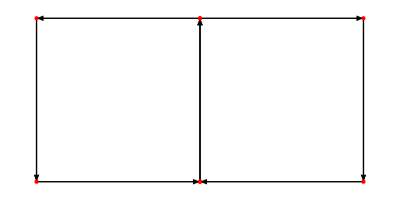
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotLoopEdges2D/@Wab[2,2]
```

## Positive matrix (3,3)

We consider trace-product of a list of Path operators. The resultant matrix should be positive definite.

```mathematica
(* the paths are truncated to type of Wab[nn, nn], where nn is the pairs of {a,-a} or {b,-b} *)
```

```mathematica
nn=4;
```

### Conjugate matrix

```mathematica
(* generate a list of path using Wab[i,j] up to i=j=nn. *)
```

```mathematica
pathList1=Table[Wab[i,j],{i,1,nn},{j,1,nn}]//Flatten[#,2]&;
pathList1//Length
```

319

```mathematica
(Wab[4,4]//Length)*4
```

140

```mathematica
(* extend the list by symmetry operators *)
```

```mathematica
pathList=Flatten[generatePathbyOper/@pathList1,1]//Union;
pathListdagger=conjugate/@pathList;
pathList//Length
```

1138

```mathematica
pathR=Prepend[pathList,{}];
pathL=Prepend[pathListdagger,{}];
ll=Length[pathL]
```

1139

```mathematica
(* Generate the positive matrix *)
```

```mathematica
MMconjugate=Monitor[
Table[Join[pathL[[ii]],pathR[[jj]]]//standardLadderLoop,{ii,ll},{jj,ll}],
Row[{
ProgressIndicator[ii,{1,ll}],ii}," "]];
%//MatrixForm
```

```mathematica
(* independent loops up to symmetry *)
```

```mathematica
MMconjugate//Flatten[#,1]&;
loopList=%//Union;
loopList//Length
```

37120

### Reflection matrix

```mathematica
pathList0=Table[Wab[i,j],{i,1,nn},{j,1,nn}]//Flatten[#,2]&;
pathList0//Length
```

319

```mathematica
pathList0=pathList0[[1;;10]];
```

```mathematica
checkPathRefSym[x_List]:=
Block[{xhalflen=Length[x]/2,x1,x2},
x1=x[[1;;xhalflen]];x2=x[[xhalflen+1;;]];
If[Count[x1,a]==Count[x1,-a]==Count[x2,a]==Count[x2,-a]&&(x1===(x2/.a->-a)||x1===(x2/.{a->-a,b->-b})),True,False]
]
```

```mathematica
checkPathRefSym/@pathList0
```

{False,False,False,True,False,False,True,False,False,False}

```mathematica
pathList1=DeleteCases[pathList0,x_/;checkPathRefSym[x]==True];
```

```mathematica
(* problematic path *)
Cases[pathList0,x_/;checkPathRefSym[x]==True]
```

{{a,b,-a,-a,-b,a},{a,b,-a,-b,-a,b,a,-b}}

```mathematica
(* generate three other paths from one path *)
```

```mathematica
generatePathbyOper[w_]:={w,w//conjugate}//Union
```

```mathematica
pathList=Flatten[generatePathbyOper/@pathList1,1]//Union;
pathList//Length
```

16

```mathematica
pathListrefconj=reflectconjugate/@pathList;
```

```mathematica
pathR=Prepend[pathList,{}];
pathL=Prepend[pathListrefconj,{}];
ll=Length[pathL]
```

17

```mathematica
(* *)
```

```mathematica
MMreflection=Table[Join[pathL[[ii]],pathR[[jj]]]//standardLadderLoop,{ii,ll},{jj,ll}];
MMreflection//MatrixForm;
```

```mathematica
MMreflection//Flatten[#,1]&;
loopListB=%//Union;
loopListB//Length
```

66

```mathematica
loopList=Join[loopList,loopListB]//Union;
```

```mathematica
loopList//Length
```

37120

### Generate SD equations

```mathematica
(* keep loops up to length 2nn*4-4 *)
```

```mathematica
loopListforSDE=DeleteCases[DeleteCases[loopList,x_/;Length[x]>(2nn*4-4)],{}];
```

```mathematica
loopListAll//Length
loopListforSDE//Length
```

0

33219

```mathematica
(* for equations that contain more than four pairs of {a,-a} or {b,-b}, we don't need to consider such equations *)
```

```mathematica
allSDE1=Monitor[
Table[{
Block[
{loop=loopListforSDE[[ii]],numa,numb},
numa=Length[Cases[loop,a]];
numb=Length[Cases[loop,b]];
(* SED will increase numa and numb by 2, so we restrict to small enough loops *)
If[numa<2nn&&numb<2nn,
bpositions=Position[loop,b]/.{x_,2}:>{x}//Flatten;
(SDESU2Red[WL@@loop,#]&/@bpositions)//Expand//Union,
{}]
]
},{ii,1,Length[loopListforSDE]}],
Row[{
ProgressIndicator[ii,{1,Length[loopListforSDE]}],ii}," "]];
```

```mathematica
allSDE1//Flatten//Length
```

64127

```mathematica
allSDE2=allSDE1//Flatten//Union;
allSDE2//Length
```

64127

```mathematica
(* Equation may contain elements that do not appear in the postive matrix, and we should exclude such equations *)
```

```mathematica
(* check if all loops in SED are belong to "loopList" *)
```

```mathematica
check[leq_]:=Block[{vars=List@@@Cases[leq//Variables,WL[__]]},If[Cases[vars,x_/;!MemberQ[loopList,x]]=={},True,False]]
```

```mathematica
allSDE3=DeleteCases[allSDE2,x_/;check[x]==False];
allSDE3//Length
```

46914

```mathematica
(* Solve SED *)
```

```mathematica
loopvars=WL@@@DeleteCases[loopList,{}];
```

```mathematica
simrule=Table[loopvars[[ii]]->w[ii],{ii,Length[loopvars]}];
```

```mathematica
simpSDE=(allSDE3/.simrule(*/.λ->1*));
simpvars=Table[w[ii],{ii,Length[loopvars]}];
```

$Aborted

```mathematica
(*Solve[(simpSDE/.λ->1)==0,simpvars][[1]];
%//Length*)
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

695

### Solving SDP

```mathematica
(* all loops in the positive matrix *)
```

```mathematica
loopvars=WL@@@DeleteCases[loopList,{}];
loopvars[[1]]
```

WL(-a,-b,a,b)

```mathematica
(* Introduce a set of new variables *)
```

```mathematica
allvars=Array[w,Length[loopvars]];
```

```mathematica
towrule1=Table[loopvars[[ii]]->w[ii],{ii,Length[loopvars]}];
```

```mathematica
towrule2=Table[List@@loopvars[[ii]]->w[ii],{ii,Length[loopvars]}]~Join~{{}->1};
```

```mathematica
(* SDE *)
```

```mathematica
loopequations=(#==0)&/@(allSDE3/.towrule1);
%//Length
```

46914

```mathematica
(* conjugate matrix *)
```

```mathematica
posimatrix1rename=MMconjugate/.towrule2;
%//MatrixForm;
```

```mathematica
(* reflection matrix *)
```

```mathematica
posimatrix2rename=MMreflection/.towrule2;
%//MatrixForm;
```

```mathematica
posimatrix1dim=Length[posimatrix1rename]
posimatrix2dim=Length[posimatrix2rename]
```

1139

17

```mathematica
(* conjugate positivity *)
```

```mathematica
(* Bootstrap the plaquee w[1]: upper bound for a given λ value *)
(*SemidefiniteOptimization[-w[1],Join[{(posimatrix1rename)(\[VectorGreaterEqual])_posimatrix1dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

```mathematica
(* Bootstrap the plaquee w[1]: lower bound for a given λ value *)
(*SemidefiniteOptimization[w[1],Join[{(posimatrix1rename)(\[VectorGreaterEqual])_posimatrix1dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

```mathematica
(* reflection positivity *)
```

```mathematica
(* Bootstrap the plaquee w[1]: upper bound for a given λ value *)
(*SemidefiniteOptimization[-w[1],Join[{(posimatrix2rename)(\[VectorGreaterEqual])_posimatrix2dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

```mathematica
(* Bootstrap the plaquee w[1]: lower bound for a given λ value *)
(*SemidefiniteOptimization[w[1],Join[{(posimatrix2rename)(\[VectorGreaterEqual])_posimatrix2dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

```mathematica
(* Join the conjugate and reflection positivity *)
```

```mathematica
(* Bootstrap the plaquee w[1]: upper bound for a given λ value *)(*SemidefiniteOptimization[-w[1],Join[{(posimatrix1rename)(\[VectorGreaterEqual])_posimatrix1dim 0},{(posimatrix2rename)(\[VectorGreaterEqual])_posimatrix2dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

```mathematica
(* Bootstrap the plaquee w[1]: lower bound for a given λ value *)(*SemidefiniteOptimization[w[1],Join[{(posimatrix1rename)(\[VectorGreaterEqual])_posimatrix1dim 0},{(posimatrix2rename)(\[VectorGreaterEqual])_posimatrix2dim 0},(-1<=#<=1)&/@allvars,loopequations]/.{λ->1},allvars];
w[1]/.%*)
```

### Plot. with reflection

#### Generate Task

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
len=5;
```

```mathematica
λvalue=Table[ii/20,{ii,1,len}];
```

```mathematica
target = Table[0,{i,1,Length[allvars]}];
target[[1]]=1;
```

```mathematica
GenerateTask[target, allvars,{posimatrix1rename,posimatrix2rename},loopequations,λ,λvalue,10^-6]
```

[Matrix] Phasing Matrices.

General::nomem: 当前计算中止，因为没有足够的内存来完成这次计算.

Throw::sysexc: 未捕捉到的 SystemException 返回顶层. 可以使用 Catch[…, _SystemException] 捕捉.

SystemException[MemoryAllocationFailure]

```mathematica
Export["allVars.wdx",allvars]
Export["posimatrix1rename.wdx",posimatrix1rename]
Export["posimatrix2rename.wdx",posimatrix2rename]
Export["loopequations.wdx",loopequations]
Export["lambda.wdx",λvalue]
```

allVars.wdx

posimatrix1rename.wdx

posimatrix2rename.wdx

loopequations.wdx

lambda.wdx